```mathematica
(*test*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\benjamin\Documents\FPII\Moessbauer\code

```mathematica
x={3.0,1.0,0.21,2.0,8.0,0.46,0.66,0.88,1.22,1.43,1.67,1.87,2.16};
names={"3.00","1.00","0.21","2.00","8.00","0.46","0.66","0.88","1.22","1.43","1.67","1.87","2.16"};
```

```mathematica
files=Flatten[Import[StringJoin["../data/background/",#,"mm.TKA"],"CSV"]]&/@names;
```

```mathematica
Dimensions[files]
```

{13,2048}

```mathematica
data=Table[{x[[j]],Sum[files[[j]][[90;;250]][[i]],{i,1,161}]/600.},{j,1,13}]
```

{{3.,27.15},{1.,30.9767},{0.21,40.5283},{2.,28.14},{8.,22.9767},{0.46,36.6067},{0.66,33.8917},{0.88,32.3133},{1.22,30.1483},{1.43,29.4067},{1.67,28.8},{1.87,28.285},{2.16,28.285}}

```mathematica
liplot=ListPlot[data];
```

```mathematica
model = a Exp[-b v]+c Exp[-d v];
```

```mathematica
nlm= NonlinearModelFit[data, model, {a,b,c,d}, v];
nlm["BestFit"]
```

16.5973 ⅇ^(-1.83855 v)+29.591 ⅇ^(-0.0313579 v)

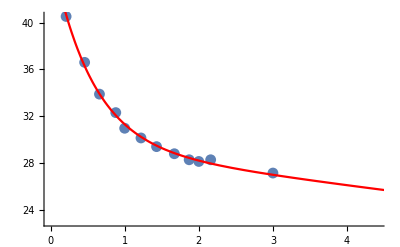

```mathematica
fit=Plot[nlm["BestFit"],{v,0,8}, PlotRange -> All,PlotStyle->Red];
Show[{liplot,fit}]
```

```mathematica
nlm["CorrelationMatrix"]//MatrixForm
```

(1. | 0.855934 | 0.00269323 | 0.822569
0.855934 | 1. | -0.112271 | 0.59205
0.00269323 | -0.112271 | 1. | 0.471837
0.822569 | 0.59205 | 0.471837 | 1.)

```mathematica
nlm[0](*Extrapoliere Untergrund*)
```

46.1884